```mathematica
s = 18;
del1 = Table[0,{s}];
del2 = Table[0,{s}];
del3 = Table[0,{s}];
```

```mathematica
Do[d = 2^(i);
l1 = d^(4/5);
l2 = d^(2/5);
c = 1/2;
del1[[i]] =1/2 * NIntegrate[1/((1 + x*l1)^(3/2)*(1 + x*l2)^(1/2) *(1 + c*x)^((d-2)/2) ) ,{x,0,Infinity}];
del2[[i]] =1/2 * NIntegrate[1/((1 + x*l2)^(3/2)*(1 + x*l1)^(1/2) *(1 + c*x)^((d-2)/2) ) ,{x,0,Infinity}];
del3[[i]] = 1/2 * NIntegrate[1/((1 + x*l2)^(1/2)*(1 + x*l1)^(1/2) *(1 +c* x)^((d-2)/2 + 1) ) ,{x,0,Infinity}];
,{i,1,s}]
```

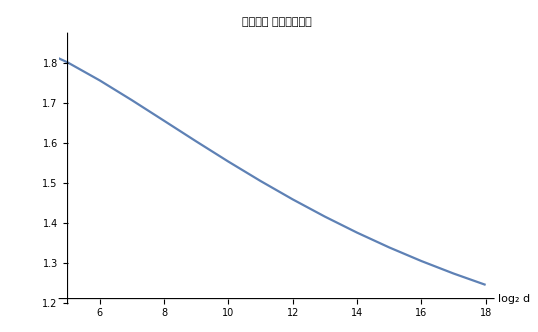

```mathematica
Show[ListLinePlot[del3/del1,PlotRange->{{5,18},Automatic}],AxesLabel->{HoldForm[Subscript[log, 2] d],None},PlotLabel->HoldForm[HoldForm[積分の比] の漸近的挙動],LabelStyle->{GrayLevel[0]}]
```

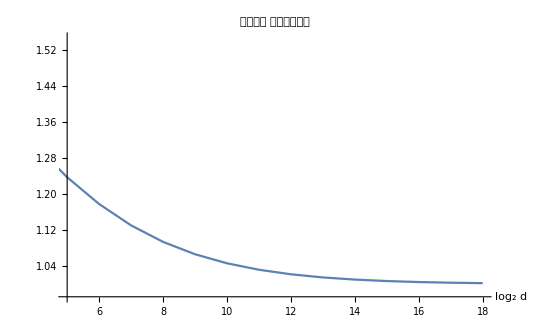

```mathematica
Show[ListLinePlot[del3/del2,PlotRange->{{5,18},Automatic}],AxesLabel->{HoldForm[Subscript[log, 2] d],None},PlotLabel->HoldForm[HoldForm[積分の比] の漸近的挙動],LabelStyle->{GrayLevel[0]}]
```